```mathematica
Clear[zx, dd,zetaHurwitz,zeta0V3Hurwitz]
delta=.01;
thetaAdd[x_,t_]:=x-t
thetaMul[x_,t_]:=x/t
thetaEq[x_,t_]:=x
f[x_,z_,k_,d_,fn_,I_]:=f[x,z,k,d,fn,I]=1+d ((z+1)/k-1) Sum[f[fn[x,d t+I],z,k+1,d,fn,I],{t,1,(x-I)/d}]
binomial[z_,k_]:=binomial[z,k]=Product[z-j,{j,0,k-1}]/k!
zx[n_,y_,z_,d_]:=zx[n,y,z,d]=If[n<y,1,Sum[d^k binomial[z,k] zx[n-k y,y+d,z-k,d],{k,0,n/y/d}]]
zx3[n_,z_,d_]:=zx[n,d,z,d]
dd[n_,0,d_]:=UnitStep[n-1]
dd[n_,k_,d_]:=dd[n,k,d]=d Sum[ dd[n/j,k-1,d],{j,1+d,n/d,d}]
ddz[n_,z_,d_]:=Sum[binomial[z,k]dd[n,k,d],{k,0,Log[1+d,n]}]
zetaHurwitz[n_,y_,0]:=UnitStep[n-1]
zetaHurwitz[n_,y_,k_]:=zetaHurwitz[n,y,k]=Sum[binomial[k,j]  zetaHurwitz[Floor[n/(m^j)],m,k-j],{j,1,k},{m,y+1,Floor[n^(1/k)]}]
zetaMinus1Scaled[n_,y_,k_]:=y^k zetaHurwitz[n y^-k,y^-1,k]
zetaScaled[n_,y_,z_]:=Expand@Sum[binomial[z,k]zetaMinus1Scaled[n,y,k],{k,0,Log[y+1,n]}]
zeta0V3Hurwitz[n_,y_,z_,d_]:=zeta0V3Hurwitz[n,y,z,d]=If[n<y,1,Sum[d^k binomial[z,k] zeta0V3Hurwitz[n/y^k,y+d,z-k,d],{k,0,Log[y,n]}]]
zeta0V3[n_,z_,d_]:=zeta0V3Hurwitz[n,1+d,z,d]
```

```mathematica
Expand@ddz[40,z,1/2]
```

1+(9523289 z)/645120+(6038543 z^2)/368640+(309147221 z^3)/46448640+(533603 z^4)/491520+(994717 z^5)/8847360+(863 z^6)/245760+(3751 z^7)/30965760+z^8/1474560+z^9/185794560

```mathematica
Expand@zeta0V3[40,z,1/2]
```

1+(9523289 z)/645120+(6038543 z^2)/368640+(309147221 z^3)/46448640+(533603 z^4)/491520+(994717 z^5)/8847360+(863 z^6)/245760+(3751 z^7)/30965760+z^8/1474560+z^9/185794560

```mathematica
Expand@f[20,z,1,1/2,thetaMul,1]
```

1+(14393 z)/1680+(92689 z^2)/11520+(96251 z^3)/46080+(5269 z^4)/18432+(1099 z^5)/92160+(23 z^6)/92160+z^7/645120

```mathematica
zetaScaled[20,0,1/2,z]
```

1+(14393 z)/1680+(92689 z^2)/11520+(96251 z^3)/46080+(5269 z^4)/18432+(1099 z^5)/92160+(23 z^6)/92160+z^7/645120

```mathematica
N[(3/2)^5]
```

7.59375

```mathematica
(7./2)^2
```

12.25

```mathematica
N@5/2*3
```

7.5

```mathematica
f[s_]:=Limit[Sum[j^-s,{j,1,x}]-Integrate[j^-s,{j,0,x}],x->Infinity]
f2[s_]:=Limit[Integrate[Floor[j]^-s-j^-s,{j,0,x}],x->Infinity]
```

```mathematica
f[2+I]
```

Zeta[2+ⅈ]

```mathematica
Integrate[Floor[j]^-s-j^-s,{j,0,Infinity}]
```

∫_0^∞ (-j^-s+Floor[j]^-s)ⅆj

```mathematica
N@Zeta[-.5+100I]
```

20.8635+0.859043 ⅈ

```mathematica
Integrate[Cos[1000 Log[j]],{j,0,x}]
```

(x (Cos[1000 Log[x]]+1000 Sin[1000 Log[x]]))/1000001

```mathematica
Integrate[Cos[0 Log[j]],{j,0,x}]
```

x

```mathematica
N@Zeta[10I]
```

1.75647-0.101512 ⅈ

```mathematica
FullSimplify[Sum[j,{j,1,Floor[x]}]-Integrate[j,{j,0,x}]]
```

1/2 (-x^2+Floor[x]+Floor[x]^2)

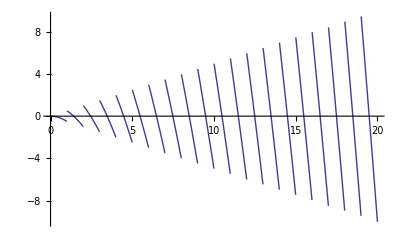

```mathematica
Plot[1/2 (-x^2+Floor[x]+Floor[x]^2),{x,0,20}]
```

```mathematica
N@Zeta[2I]
```

0.314726-0.23168 ⅈ

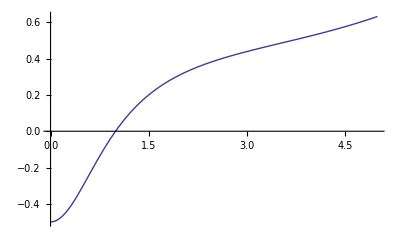

```mathematica
Plot[Re@Zeta[s I],{s,0,5}]
```

```mathematica
Integrate[Sin[1000 Log[t]],{t,0,x}]
```

(x (-1000 Cos[1000 Log[x]]+Sin[1000 Log[x]]))/1000001

```mathematica
Integrate[ Sin[1000 Log[t]],t]
```

-(1000 t Cos[1000 Log[t]])/1000001+(t Sin[1000 Log[t]])/1000001

```mathematica
(1000 Log[5.]-1000 Log[4.])/(2 Pi)
```

35.5144

```mathematica
N@Table[{x,(1000 Log[x+1]-1000 Log[x])/(2 Pi)},{x,2,80}]//TableForm
```

2. | 64.5318
3. | 45.786
4. | 35.5144
5. | 29.0174
6. | 24.5338
7. | 21.2522
8. | 18.7458
9. | 16.7686
10. | 15.1691
11. | 13.8483
12. | 12.7392
13. | 11.7947
14. | 10.9806
15. | 10.2716
16. | 9.64871
17. | 9.09704
18. | 8.60507
19. | 8.16358
20. | 7.7652
21. | 7.40389
22. | 7.07472
23. | 6.77357
24. | 6.49702
25. | 6.24217
26. | 6.00656
27. | 5.78809
28. | 5.58496
29. | 5.3956
30. | 5.21866
31. | 5.05296
32. | 4.89746
33. | 4.75125
34. | 4.61351
35. | 4.48353
36. | 4.36068
37. | 4.24438
38. | 4.13413
39. | 4.02945
40. | 3.92995
41. | 3.83524
42. | 3.74499
43. | 3.6589
44. | 3.57667
45. | 3.49805
46. | 3.42282
47. | 3.35075
48. | 3.28166
49. | 3.21536
50. | 3.15169
51. | 3.09048
52. | 3.03161
53. | 2.97495
54. | 2.92036
55. | 2.86773
56. | 2.81698
57. | 2.76798
58. | 2.72066
59. | 2.67494
60. | 2.63072
61. | 2.58794
62. | 2.54653
63. | 2.50643
64. | 2.46757
65. | 2.42989
66. | 2.39335
67. | 2.35789
68. | 2.32347
69. | 2.29004
70. | 2.25755
71. | 2.22598
72. | 2.19528
73. | 2.16541
74. | 2.13634
75. | 2.10804
76. | 2.08049
77. | 2.05364
78. | 2.02748
79. | 2.00198
80. | 1.97711

```mathematica
E^(Log[x]+8Pi/1000)
```

ⅇ^(π/125) x

```mathematica
N[1/(E^(8Pi/1000)-1)]
```

39.2908

```mathematica
FullSimplify[1/(E^((2 Pi s)/f)-1)]
```

1/2 (-1+Coth[(π s)/f])

```mathematica
Table[ N[1/2 (-1+Coth[(π s)/f])/.f->10000],{s,0,10, 1/2}]
```

{ComplexInfinity,3182.6,1591.05,1060.53,795.275,636.12,530.017,454.229,397.388,353.178,317.81,288.873,264.759,244.354,226.865,211.707,198.444,186.742,176.339,167.032,158.655}

```mathematica
N@Table[{x,(1000 Log[x+1]-1000 Log[x])/(2 Pi)},{x,147,172}]//TableForm
```

147. | 1.07902
148. | 1.07175
149. | 1.06459
150. | 1.05751
151. | 1.05053
152. | 1.04364
153. | 1.03684
154. | 1.03013
155. | 1.02351
156. | 1.01697
157. | 1.01051
158. | 1.00414
159. | 0.99784
160. | 0.991623
161. | 0.985483
162. | 0.979418
163. | 0.973428
164. | 0.96751
165. | 0.961664
166. | 0.955888
167. | 0.950182
168. | 0.944542
169. | 0.93897
170. | 0.933463
171. | 0.92802
172. | 0.92264

```mathematica
N@Zeta[50000I]
```

82.6139+69.0695 ⅈ